# QFT compilation

## Toy device

Connectivity

Native gates: Rx_j[θ],  Ry_j[θ], C_i[Z_(i+1)],Meas, Init,  Wait_-1[Δt]

Modules

```mathematica
(*Test for the variety of the initial states *)
checkVariation[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
(*Print[i,":",a];*)
ToString[Reverse@Sort[Length/@a]]
]

checkedConf[dev_,unitary_,ntrainstates_]:=Module[{conf,a},
While[True,
DestroyAllQuregs[];
conf=DefaultConfig[dev,unitary,ntrainstates];
a=Gather[Times@@#&/@Values[varMeanInitStates[conf]],Abs[#1-#2]<=10^-4&];
If[AllTrue[Length/@a,#==1&],
Break[]]
];
conf
]
```

```mathematica
SetAttributes[CompileCirc,HoldAll]
CompileCirc[conf_,unitary_,qubitsnum_,list_]:=Module[{nansatz,simpncirc,fdist,ρ,qubits,ancillas,bells,ψ,uqubits},
{time,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}}=Timing[CircuitSynthesis[qubitsnum,conf]];
AppendTo[list,{conf,time,Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,probzeros,qmiavg,elimmerge,elimbfsmall,elimmetov,elimbf}];

nansatz=noisyAnsatz[ansatz/.θvars,conf];
simpncirc=SimplifyCircuit[DeleteCases[DeleteCases[nansatz,Subscript[Depol, __][0.]],Subscript[Deph, __][0.]]];
(* Fidelity distance *)
ρ=CreateDensityQureg[qubitsnum*2];
ψ=CreateQureg[qubitsnum*2];
uqubits=Range[0,-1+IntegerPart[Log2@Length@unitary]];
qubits=Range[0,qubitsnum-1];
ancillas=Range[qubitsnum,qubitsnum*2-1];
bells=Flatten[{Subscript[H, #[[1]]],Subscript[C, #[[1]]][Subscript[X, #[[2]]]]}&/@(Transpose[{qubits,ancillas}])];
ApplyCircuit[ρ,bells];
ApplyCircuit[ψ,bells];
ApplyCircuit[ρ,{Subscript[U, Sequence@@uqubits][ConjugateTranspose@unitary]}];
ApplyCircuit[ρ,simpncirc];

fdist=1-CalcFidelity[ρ,ψ];
DestroyQureg[ρ];
DestroyQureg[ψ];

Print["compile time:",time/60," minutes; total iterations ",fev];
Print@ListPlot[Elist,AxesLabel->{"Successful iteration","Cost"}];
Print@DrawCircuit[ansatz,qubitsnum];
Print["prob(0):",probzeros];
Print["dist_fid=",fdist]
]
```

```mathematica
QFT[nqubit_,swap_:False]:=Flatten@Join[{If[swap,Table[Subscript[SWAP, i,nqubit-i-1],{i,0,IntegerPart[nqubit/2]-1}],{}],{Subscript[H, 0]}},Table[Join[Table[Subscript[C, m][Subscript[Ph, i][π 2^(-m-1)]],{m,0,i-1}],{Subscript[H, i]}],{i,1,nqubit-1}]]
```

## 4 qubit QFT

```mathematica
qubitsnum=4;
nt=7;
```

```mathematica
Graph[Range[0,qubitsnum-1],Table[j<->j+1,{j,0,qubitsnum-2}],VertexLabels->Placed[Automatic,Center],VertexSize->.5]
```

-Graphics-

## Clean device

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->1,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{0,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->1,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{0,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->10
};
```

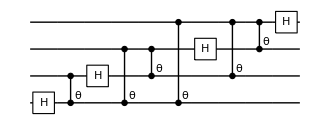

```mathematica
DrawCircuit[QFT[qubitsnum]]
```

Finite difference

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 16:09:25, fev:509, <E>: 0.15119504606137837 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 38, 0, 2, 16}

@cycle2:Sat 17 Sep 2022 16:21:16, fev:817, <E>: 0.10941337462100341 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 2, 21}

@cycle3:Sat 17 Sep 2022 16:28:21, fev:1005, <E>: 0.10538449066487596 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 67, 0, 9, 25}

I'm slowing down @cycle 4

@cycle4:Sat 17 Sep 2022 16:31:40, fev:1063, <E>: 0.10538449066487596 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 67, 0, 9, 31}

@cycle5:Sat 17 Sep 2022 16:58:32, fev:1379, <E>: 0.09309742380495492 nansatz: 48 merged-smallθ-metric-bf-gmerged: {1, 88, 0, 9, 40}

@cycle6:Sat 17 Sep 2022 17:39:46, fev:1782, <E>: 0.08017956755447164 nansatz: 37 merged-smallθ-metric-bf-gmerged: {2, 139, 0, 9, 53}

@cycle7:Sat 17 Sep 2022 18:13:59, fev:2162, <E>: 0.05975446755866303 nansatz: 36 merged-smallθ-metric-bf-gmerged: {3, 180, 0, 10, 62}

@cycle8:Sat 17 Sep 2022 18:38:25, fev:2403, <E>: 0.05424039176594047 nansatz: 55 merged-smallθ-metric-bf-gmerged: {3, 202, 0, 10, 70}

@cycle9:Sat 17 Sep 2022 19:40:36, fev:3009, <E>: 0.03555067281946584 nansatz: 41 merged-smallθ-metric-bf-gmerged: {3, 257, 0, 11, 81}

@cycle10:Sat 17 Sep 2022 20:10:31, fev:3405, <E>: 0.006863203668723399 nansatz: 29 merged-smallθ-metric-bf-gmerged: {3, 305, 0, 11, 93}

@cycle11:Sat 17 Sep 2022 20:39:40, fev:3836, <E>: 0.0014467676606591579 nansatz: 30 merged-smallθ-metric-bf-gmerged: {3, 337, 0, 12, 109}

@cycle12:Sat 17 Sep 2022 21:07:30, fev:4218, <E>: 0.0005223445032501083 nansatz: 32 merged-smallθ-metric-bf-gmerged: {3, 375, 0, 12, 127}

@cycle13:Sat 17 Sep 2022 21:41:51, fev:4670, <E>: 7.682984961403041e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {3, 409, 0, 12, 140}

I'm slowing down @cycle 14

@cycle14:Sat 17 Sep 2022 22:03:38, fev:4919, <E>: 7.682984961403041e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {3, 409, 0, 12, 154}

I'm slowing down @cycle 15

@cycle15:Sat 17 Sep 2022 22:43:04, fev:5183, <E>: 7.682984961403041e-6 nansatz: 33 merged-smallθ-metric-bf-gmerged: {3, 409, 0, 12, 185}

compile time:2105.56 minutes; total iterations 5653

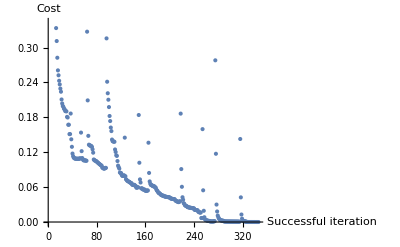

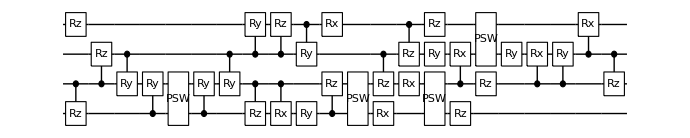

prob(0):<|0→0.25,1→0.249999,2→0.25,3→0.25|>

dist_fid=0.0000181849

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 23:26:49, fev:435, <E>: 0.3327750554880099 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 0, 21}

@cycle2:Sat 17 Sep 2022 23:37:25, fev:698, <E>: 0.21626185641390253 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 61, 0, 0, 26}

@cycle3:Sat 17 Sep 2022 23:46:37, fev:885, <E>: 0.1617980222956768 nansatz: 33 merged-smallθ-metric-bf-gmerged: {0, 70, 0, 0, 27}

@cycle4:Sun 18 Sep 2022 00:00:59, fev:1141, <E>: 0.04930073632817721 nansatz: 28 merged-smallθ-metric-bf-gmerged: {3, 95, 0, 1, 32}

@cycle5:Sun 18 Sep 2022 00:12:25, fev:1382, <E>: 0.03400502631916437 nansatz: 31 merged-smallθ-metric-bf-gmerged: {5, 108, 0, 1, 37}

@cycle6:Sun 18 Sep 2022 00:22:26, fev:1555, <E>: 0.030287508952197065 nansatz: 37 merged-smallθ-metric-bf-gmerged: {5, 120, 0, 1, 46}

@cycle7:Sun 18 Sep 2022 00:38:48, fev:1802, <E>: 0.024781738657076124 nansatz: 45 merged-smallθ-metric-bf-gmerged: {5, 130, 0, 1, 51}

@cycle8:Sun 18 Sep 2022 01:02:07, fev:2072, <E>: 0.01976017611648955 nansatz: 54 merged-smallθ-metric-bf-gmerged: {5, 139, 0, 2, 56}

@cycle9:Sun 18 Sep 2022 01:36:00, fev:2512, <E>: 0.011311874743176306 nansatz: 36 merged-smallθ-metric-bf-gmerged: {6, 176, 0, 2, 64}

@cycle10:Sun 18 Sep 2022 01:55:51, fev:2839, <E>: 0.007985908583370342 nansatz: 39 merged-smallθ-metric-bf-gmerged: {6, 189, 0, 2, 75}

@cycle11:Sun 18 Sep 2022 02:12:02, fev:3072, <E>: 0.005430893406826343 nansatz: 49 merged-smallθ-metric-bf-gmerged: {6, 196, 0, 2, 89}

@cycle12:Sun 18 Sep 2022 02:46:28, fev:3503, <E>: 0.003390676753381378 nansatz: 45 merged-smallθ-metric-bf-gmerged: {6, 219, 0, 2, 99}

@cycle13:Sun 18 Sep 2022 03:13:54, fev:3825, <E>: 0.0028831637470844757 nansatz: 50 merged-smallθ-metric-bf-gmerged: {7, 232, 0, 3, 109}

@cycle14:Sun 18 Sep 2022 03:58:16, fev:4441, <E>: 0.000017663698559160024 nansatz: 35 merged-smallθ-metric-bf-gmerged: {7, 264, 0, 4, 127}

@cycle15:Sun 18 Sep 2022 04:20:11, fev:4824, <E>: 7.094572921025254e-6 nansatz: 36 merged-smallθ-metric-bf-gmerged: {7, 281, 0, 4, 137}

I'm slowing down @cycle 16

@cycle16:Sun 18 Sep 2022 04:34:16, fev:5057, <E>: 7.094572921025254e-6 nansatz: 36 merged-smallθ-metric-bf-gmerged: {7, 281, 0, 4, 148}

I'm slowing down @cycle 17

@cycle17:Sun 18 Sep 2022 04:54:06, fev:5281, <E>: 7.094572921025254e-6 nansatz: 36 merged-smallθ-metric-bf-gmerged: {7, 281, 0, 4, 175}

compile time:2241.36 minutes; total iterations 6851

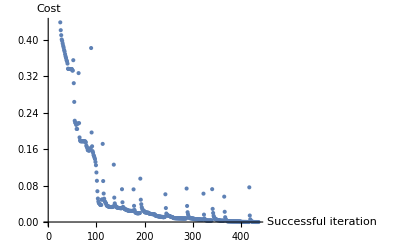

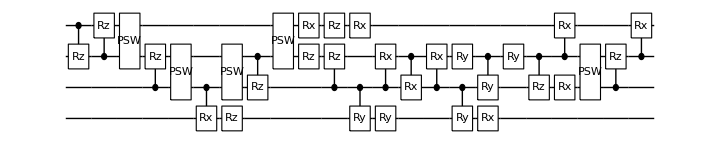

prob(0):<|0→0.250001,1→0.25,2→0.25,3→0.25|>

dist_fid=0.0000284579

Compilation with automatically generated ansatz

@cycle1:Sun 18 Sep 2022 06:05:35, fev:364, <E>: 0.2388921464189438 nansatz: 51 merged-smallθ-metric-bf-gmerged: {1, 4, 0, 0, 31}

@cycle2:Sun 18 Sep 2022 06:40:37, fev:844, <E>: 0.09650330129092057 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 49, 0, 0, 41}

@cycle3:Sun 18 Sep 2022 06:56:26, fev:1182, <E>: 0.026010036453423292 nansatz: 31 merged-smallθ-metric-bf-gmerged: {3, 67, 0, 0, 46}

@cycle4:Sun 18 Sep 2022 07:18:10, fev:1607, <E>: 0.007479970685501206 nansatz: 34 merged-smallθ-metric-bf-gmerged: {4, 82, 0, 0, 53}

@cycle5:Sun 18 Sep 2022 07:40:07, fev:1998, <E>: 0.00324020764125025 nansatz: 38 merged-smallθ-metric-bf-gmerged: {4, 98, 0, 0, 62}

@cycle6:Sun 18 Sep 2022 08:04:35, fev:2435, <E>: 0.001486518942029526 nansatz: 38 merged-smallθ-metric-bf-gmerged: {4, 117, 0, 0, 68}

@cycle7:Sun 18 Sep 2022 08:36:30, fev:2987, <E>: 0.00019200527999710393 nansatz: 40 merged-smallθ-metric-bf-gmerged: {4, 133, 0, 0, 80}

@cycle8:Sun 18 Sep 2022 09:11:39, fev:3566, <E>: 0.00006348747063129283 nansatz: 43 merged-smallθ-metric-bf-gmerged: {4, 150, 0, 0, 84}

@cycle9:Sun 18 Sep 2022 09:43:00, fev:4045, <E>: 0.000017215477725865797 nansatz: 42 merged-smallθ-metric-bf-gmerged: {5, 166, 0, 0, 94}

I'm slowing down @cycle 10

@cycle10:Sun 18 Sep 2022 09:57:10, fev:4254, <E>: 0.000017215477725865797 nansatz: 42 merged-smallθ-metric-bf-gmerged: {5, 166, 0, 0, 103}

I'm slowing down @cycle 11

@cycle11:Sun 18 Sep 2022 10:20:46, fev:4500, <E>: 0.000017215477725865797 nansatz: 42 merged-smallθ-metric-bf-gmerged: {5, 166, 0, 0, 118}

compile time:2082.85 minutes; total iterations 5554

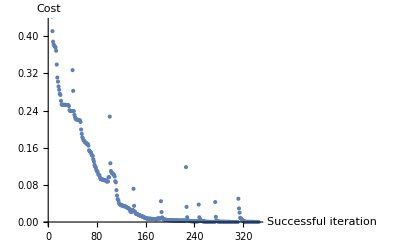

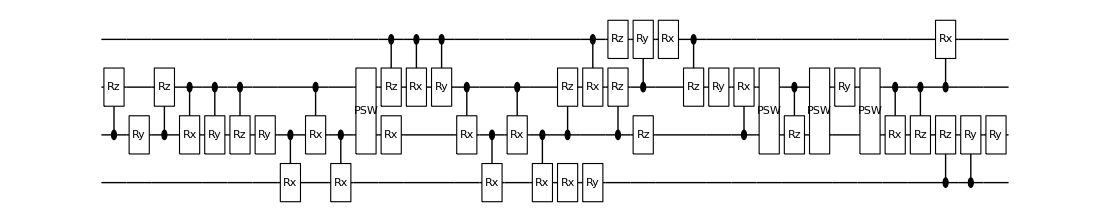

prob(0):<|0→0.250001,1→0.249999,2→0.249999,3→0.250001|>

dist_fid=0.437519

Compilation with automatically generated ansatz

@cycle1:Sun 18 Sep 2022 11:43:35, fev:412, <E>: 0.2526826765656746 nansatz: 38 merged-smallθ-metric-bf-gmerged: {2, 19, 0, 0, 22}

@cycle2:Sun 18 Sep 2022 11:59:05, fev:706, <E>: 0.13427964932909625 nansatz: 27 merged-smallθ-metric-bf-gmerged: {2, 56, 0, 0, 34}

@cycle3:Sun 18 Sep 2022 12:12:11, fev:950, <E>: 0.10134779200086406 nansatz: 34 merged-smallθ-metric-bf-gmerged: {2, 71, 0, 0, 41}

@cycle4:Sun 18 Sep 2022 12:24:04, fev:1134, <E>: 0.08162548133208329 nansatz: 41 merged-smallθ-metric-bf-gmerged: {3, 85, 0, 0, 53}

@cycle5:Sun 18 Sep 2022 12:38:47, fev:1358, <E>: 0.07070162622429219 nansatz: 33 merged-smallθ-metric-bf-gmerged: {5, 111, 0, 0, 60}

@cycle6:Sun 18 Sep 2022 12:55:32, fev:1658, <E>: 0.0600542415473398 nansatz: 33 merged-smallθ-metric-bf-gmerged: {5, 132, 0, 0, 70}

@cycle7:Sun 18 Sep 2022 13:09:37, fev:1887, <E>: 0.053782977444269076 nansatz: 40 merged-smallθ-metric-bf-gmerged: {5, 144, 0, 0, 77}

@cycle8:Sun 18 Sep 2022 13:26:41, fev:2127, <E>: 0.052348894767170195 nansatz: 41 merged-smallθ-metric-bf-gmerged: {5, 162, 0, 0, 82}

@cycle9:Sun 18 Sep 2022 13:42:13, fev:2313, <E>: 0.0500470433251068 nansatz: 53 merged-smallθ-metric-bf-gmerged: {5, 172, 0, 0, 84}

$Aborted

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy0={};
Table[
conf=checkedConf[dev,unitary,nt];
CompileCirc[conf,unitary,qubitsnum,toy0]
,{5}];
```

Compilation with automatically generated ansatz at Sun 18 Sep 2022 13:53:23

@cycle1:Sun 18 Sep 2022 14:30:03, fev:342, <E>: 0.19577855489187543 nansatz: 50 merged-smallθ-metric-bf-gmerged: {2, 7, 0, 0, 28}

@cycle2:Sun 18 Sep 2022 15:13:16, fev:705, <E>: 0.07805081333721924 nansatz: 33 merged-smallθ-metric-bf-gmerged: {5, 46, 0, 0, 42}

@cycle3:Sun 18 Sep 2022 15:33:34, fev:1014, <E>: 0.02971853618727054 nansatz: 31 merged-smallθ-metric-bf-gmerged: {5, 65, 0, 0, 51}

@cycle4:Sun 18 Sep 2022 15:52:16, fev:1233, <E>: 0.022725290874933562 nansatz: 37 merged-smallθ-metric-bf-gmerged: {5, 80, 0, 1, 56}

@cycle5:Sun 18 Sep 2022 16:12:14, fev:1432, <E>: 0.022494120112485503 nansatz: 46 merged-smallθ-metric-bf-gmerged: {6, 88, 0, 1, 61}

@cycle6:Sun 18 Sep 2022 16:45:05, fev:1740, <E>: 0.0178923799755235 nansatz: 37 merged-smallθ-metric-bf-gmerged: {9, 112, 0, 1, 64}

@cycle7:Sun 18 Sep 2022 17:03:22, fev:1931, <E>: 0.014897137105178402 nansatz: 41 merged-smallθ-metric-bf-gmerged: {9, 127, 0, 1, 66}

@cycle8:Sun 18 Sep 2022 17:31:09, fev:2346, <E>: 0.011108647142826333 nansatz: 28 merged-smallθ-metric-bf-gmerged: {9, 160, 0, 1, 71}

@cycle9:Sun 18 Sep 2022 17:51:37, fev:2656, <E>: 0.0043725769374427835 nansatz: 31 merged-smallθ-metric-bf-gmerged: {9, 177, 0, 1, 85}

@cycle10:Sun 18 Sep 2022 18:19:38, fev:3081, <E>: 0.0007697240392338021 nansatz: 32 merged-smallθ-metric-bf-gmerged: {9, 194, 0, 1, 99}

@cycle11:Sun 18 Sep 2022 18:43:49, fev:3429, <E>: 2.44384518667738e-6 nansatz: 32 merged-smallθ-metric-bf-gmerged: {9, 211, 0, 1, 114}

I'm slowing down @cycle 12

@cycle12:Sun 18 Sep 2022 19:03:10, fev:3649, <E>: 2.44384518667738e-6 nansatz: 32 merged-smallθ-metric-bf-gmerged: {9, 211, 0, 1, 126}

I'm slowing down @cycle 13

@cycle13:Sun 18 Sep 2022 19:35:47, fev:3888, <E>: 2.44384518667738e-6 nansatz: 32 merged-smallθ-metric-bf-gmerged: {9, 211, 0, 1, 137}

compile time:1437.96 minutes; total iterations 4388

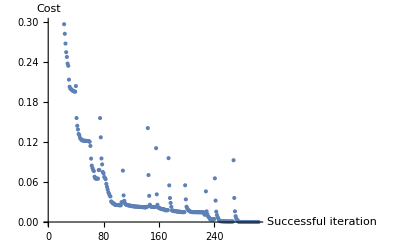

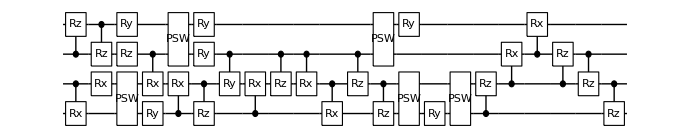

prob(0):<|0→0.25,1→0.25,2→0.25,3→0.25|>

dist_fid=0.0000115225

Compilation with automatically generated ansatz at Sun 18 Sep 2022 19:51:30

@cycle1:Sun 18 Sep 2022 20:19:50, fev:328, <E>: 0.24569741880499338 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 35, 0, 0, 14}

@cycle2:Sun 18 Sep 2022 20:34:11, fev:582, <E>: 0.18658052748080176 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 27}

@cycle3:Sun 18 Sep 2022 20:53:55, fev:853, <E>: 0.12159089095087128 nansatz: 35 merged-smallθ-metric-bf-gmerged: {0, 69, 0, 0, 34}

$Aborted

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Table[
conf=checkedConf[dev,unitary,nt];
CompileCirc[conf,unitary,qubitsnum,toy0]
,{3}];
```

Compilation with automatically generated ansatz at Sun 18 Sep 2022 21:19:00

@cycle1:Sun 18 Sep 2022 21:51:53, fev:345, <E>: 0.16754615934901093 nansatz: 30 merged-smallθ-metric-bf-gmerged: {0, 28, 0, 0, 17}

@cycle2:Sun 18 Sep 2022 22:09:44, fev:649, <E>: 0.06747658608976992 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 58, 0, 0, 25}

@cycle3:Sun 18 Sep 2022 22:21:49, fev:899, <E>: 0.03090789053712394 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 77, 0, 0, 37}

@cycle4:Sun 18 Sep 2022 22:32:09, fev:1095, <E>: 0.026317714615010524 nansatz: 24 merged-smallθ-metric-bf-gmerged: {0, 95, 0, 1, 43}

@cycle5:Sun 18 Sep 2022 22:40:56, fev:1214, <E>: 0.02521455148009416 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 96, 0, 1, 44}

I'm slowing down @cycle 6

@cycle6:Sun 18 Sep 2022 22:48:54, fev:1282, <E>: 0.02521455148009416 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 96, 0, 1, 50}

I'm slowing down @cycle 7

@cycle7:Sun 18 Sep 2022 23:02:05, fev:1363, <E>: 0.02521455148009416 nansatz: 42 merged-smallθ-metric-bf-gmerged: {0, 96, 0, 1, 65}

compile time:654.159 minutes; total iterations 1908

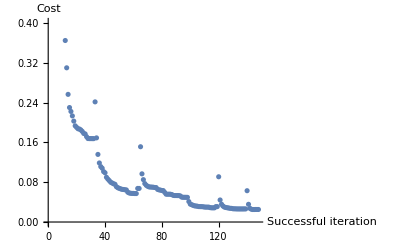

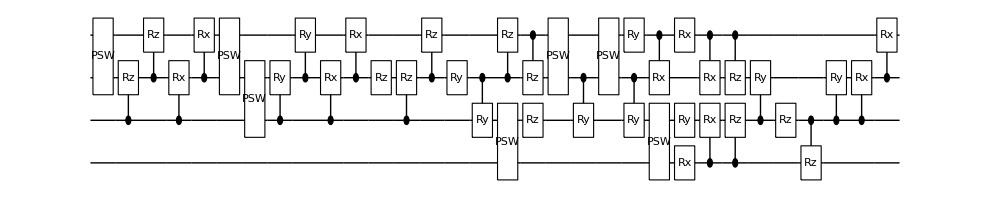

prob(0):<|0→0.2529,1→0.245575,2→0.252389,3→0.249136|>

dist_fid=0.0464953

Compilation with automatically generated ansatz at Sun 18 Sep 2022 23:42:59

@cycle1:Mon 19 Sep 2022 00:08:21, fev:262, <E>: 0.3339775639960635 nansatz: 31 merged-smallθ-metric-bf-gmerged: {1, 26, 0, 0, 19}

@cycle2:Mon 19 Sep 2022 00:35:45, fev:603, <E>: 0.10568994965887916 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 51, 0, 0, 33}

@cycle3:Mon 19 Sep 2022 00:59:44, fev:999, <E>: 0.04184460970538555 nansatz: 22 merged-smallθ-metric-bf-gmerged: {1, 81, 0, 0, 39}

@cycle4:Mon 19 Sep 2022 01:10:05, fev:1212, <E>: 0.034135439807129124 nansatz: 23 merged-smallθ-metric-bf-gmerged: {1, 99, 0, 0, 44}

@cycle5:Mon 19 Sep 2022 01:20:48, fev:1427, <E>: 0.03213265846951393 nansatz: 30 merged-smallθ-metric-bf-gmerged: {2, 111, 0, 0, 52}

@cycle6:Mon 19 Sep 2022 01:32:30, fev:1621, <E>: 0.026679089901084117 nansatz: 25 merged-smallθ-metric-bf-gmerged: {2, 135, 0, 0, 59}

@cycle7:Mon 19 Sep 2022 01:48:40, fev:1826, <E>: 0.02607606120005652 nansatz: 43 merged-smallθ-metric-bf-gmerged: {2, 139, 0, 0, 62}

@cycle8:Mon 19 Sep 2022 02:32:04, fev:2333, <E>: 0.009372135828658316 nansatz: 29 merged-smallθ-metric-bf-gmerged: {3, 172, 0, 0, 65}

@cycle9:Mon 19 Sep 2022 02:49:39, fev:2569, <E>: 0.0015947948985448998 nansatz: 31 merged-smallθ-metric-bf-gmerged: {3, 190, 0, 0, 76}

@cycle10:Mon 19 Sep 2022 03:05:47, fev:2786, <E>: 1.978795037803151e-6 nansatz: 31 merged-smallθ-metric-bf-gmerged: {3, 206, 0, 0, 84}

I'm slowing down @cycle 11

@cycle11:Mon 19 Sep 2022 03:20:55, fev:2961, <E>: 1.978795037803151e-6 nansatz: 31 merged-smallθ-metric-bf-gmerged: {3, 206, 0, 0, 87}

I'm slowing down @cycle 12

@cycle12:Mon 19 Sep 2022 03:44:06, fev:3137, <E>: 1.978795037803151e-6 nansatz: 31 merged-smallθ-metric-bf-gmerged: {3, 206, 0, 0, 96}

compile time:1029.84 minutes; total iterations 3472

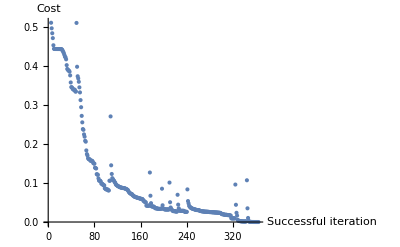

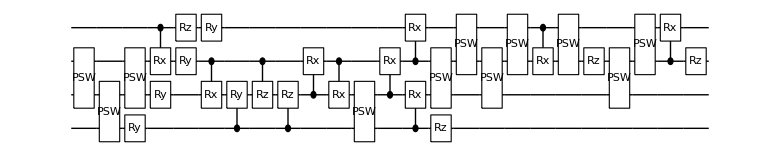

prob(0):<|0→0.25,1→0.25,2→0.25,3→0.25|>

dist_fid=6.77272×10^-6

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
Table[
conf=checkedConf[dev,unitary,nt];
CompileCirc[conf,unitary,qubitsnum,toy0]
,{2}];
```

## Small error: gate fidelity: 0.9999, T1=10^5,T2=100

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->100,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.9999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.9999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->1
};
```

Compilation with automatically generated ansatz at Mon 19 Sep 2022 03:55:07

@cycle1:Mon 19 Sep 2022 04:32:05, fev:457, <E>: 0.26520914536485923 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 40, 0, 0, 15}

@cycle2:Mon 19 Sep 2022 04:43:46, fev:716, <E>: 0.19634766450883778 nansatz: 23 merged-smallθ-metric-bf-gmerged: {0, 59, 0, 0, 21}

@cycle3:Mon 19 Sep 2022 05:00:29, fev:976, <E>: 0.1434709562311582 nansatz: 32 merged-smallθ-metric-bf-gmerged: {1, 71, 0, 0, 25}

@cycle4:Mon 19 Sep 2022 05:26:08, fev:1403, <E>: 0.1280712315523255 nansatz: 29 merged-smallθ-metric-bf-gmerged: {1, 97, 0, 0, 31}

@cycle5:Mon 19 Sep 2022 05:47:55, fev:1677, <E>: 0.11456608054768523 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 111, 0, 0, 42}

I'm slowing down @cycle 6

@cycle6:Mon 19 Sep 2022 05:56:20, fev:1751, <E>: 0.11456608054768523 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 111, 0, 0, 45}

I'm slowing down @cycle 7

@cycle7:Mon 19 Sep 2022 06:08:21, fev:1818, <E>: 0.11456608054768523 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 111, 0, 0, 55}

compile time:661.071 minutes; total iterations 2181

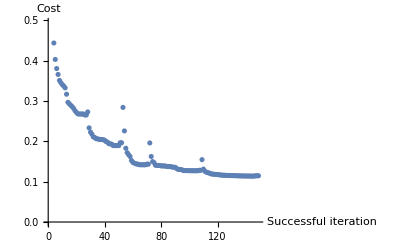

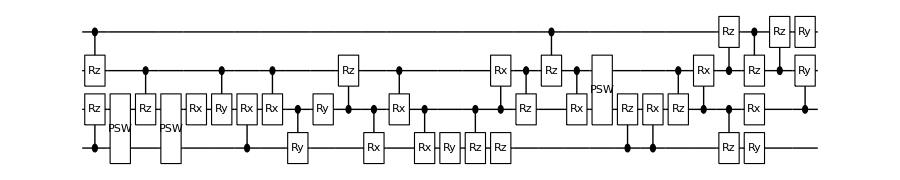

prob(0):<|0→0.238476,1→0.255016,2→0.260167,3→0.246341|>

dist_fid=0.548261

Compilation with automatically generated ansatz at Mon 19 Sep 2022 06:31:36

@cycle1:Mon 19 Sep 2022 07:01:39, fev:418, <E>: 0.28209606789821184 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 45, 0, 0, 22}

@cycle2:Mon 19 Sep 2022 07:10:42, fev:631, <E>: 0.18227370739883858 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 64, 0, 0, 34}

@cycle3:Mon 19 Sep 2022 07:25:04, fev:882, <E>: 0.13971286421604182 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 79, 0, 0, 44}

@cycle4:Mon 19 Sep 2022 07:35:47, fev:1078, <E>: 0.07383939906486026 nansatz: 22 merged-smallθ-metric-bf-gmerged: {2, 102, 0, 0, 56}

@cycle5:Mon 19 Sep 2022 07:45:54, fev:1290, <E>: 0.01778044537871965 nansatz: 21 merged-smallθ-metric-bf-gmerged: {2, 123, 0, 0, 61}

@cycle6:Mon 19 Sep 2022 07:55:20, fev:1507, <E>: 0.004453664695552195 nansatz: 23 merged-smallθ-metric-bf-gmerged: {2, 140, 0, 0, 72}

@cycle7:Mon 19 Sep 2022 08:08:29, fev:1736, <E>: 0.0018234782534744412 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 159, 0, 0, 80}

I'm slowing down @cycle 8

@cycle8:Mon 19 Sep 2022 08:20:20, fev:1895, <E>: 0.0018234782534744412 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 159, 0, 0, 82}

I'm slowing down @cycle 9

@cycle9:Mon 19 Sep 2022 08:47:36, fev:2122, <E>: 0.0018234782534744412 nansatz: 24 merged-smallθ-metric-bf-gmerged: {2, 159, 0, 0, 92}

compile time:554.64 minutes; total iterations 2381

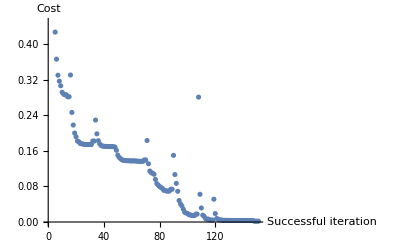

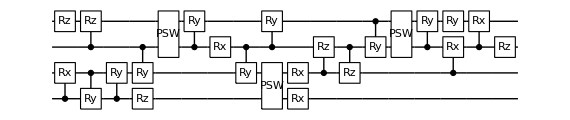

prob(0):<|0→0.250072,1→0.250033,2→0.249977,3→0.249918|>

dist_fid=0.00317552

Compilation with automatically generated ansatz at Mon 19 Sep 2022 08:52:55

@cycle1:Mon 19 Sep 2022 09:27:38, fev:325, <E>: 0.22235352381938492 nansatz: 35 merged-smallθ-metric-bf-gmerged: {1, 21, 0, 0, 20}

@cycle2:Mon 19 Sep 2022 09:55:15, fev:614, <E>: 0.20101205654120374 nansatz: 34 merged-smallθ-metric-bf-gmerged: {2, 44, 0, 2, 31}

@cycle3:Mon 19 Sep 2022 10:18:22, fev:943, <E>: 0.18830250384516795 nansatz: 19 merged-smallθ-metric-bf-gmerged: {6, 78, 0, 2, 36}

@cycle4:Mon 19 Sep 2022 10:28:19, fev:1134, <E>: 0.14873282995876766 nansatz: 23 merged-smallθ-metric-bf-gmerged: {6, 96, 0, 2, 42}

@cycle5:Mon 19 Sep 2022 10:39:36, fev:1271, <E>: 0.13171686021369414 nansatz: 39 merged-smallθ-metric-bf-gmerged: {6, 102, 0, 2, 44}

@cycle6:Mon 19 Sep 2022 11:01:30, fev:1471, <E>: 0.12460109555437811 nansatz: 41 merged-smallθ-metric-bf-gmerged: {7, 122, 0, 3, 47}

@cycle7:Mon 19 Sep 2022 11:22:56, fev:1695, <E>: 0.12335529520645501 nansatz: 30 merged-smallθ-metric-bf-gmerged: {8, 153, 0, 3, 60}

@cycle8:Mon 19 Sep 2022 11:34:07, fev:1857, <E>: 0.11419275462978908 nansatz: 29 merged-smallθ-metric-bf-gmerged: {8, 171, 0, 3, 73}

@cycle9:Mon 19 Sep 2022 11:48:13, fev:2047, <E>: 0.11233597237986351 nansatz: 29 merged-smallθ-metric-bf-gmerged: {9, 190, 0, 3, 79}

@cycle10:Mon 19 Sep 2022 12:03:34, fev:2210, <E>: 0.10436834759675047 nansatz: 40 merged-smallθ-metric-bf-gmerged: {11, 198, 0, 3, 85}

@cycle11:Mon 19 Sep 2022 12:23:24, fev:2356, <E>: 0.10341180885422883 nansatz: 52 merged-smallθ-metric-bf-gmerged: {11, 207, 0, 3, 89}

@cycle12:Mon 19 Sep 2022 12:51:08, fev:2501, <E>: 0.09000567264905332 nansatz: 63 merged-smallθ-metric-bf-gmerged: {12, 218, 0, 3, 95}

I'm slowing down @cycle 13

@cycle13:Mon 19 Sep 2022 13:09:54, fev:2593, <E>: 0.09000567264905332 nansatz: 63 merged-smallθ-metric-bf-gmerged: {12, 218, 0, 3, 104}

@cycle14:Mon 19 Sep 2022 14:49:51, fev:2954, <E>: 0.08658620793697806 nansatz: 69 merged-smallθ-metric-bf-gmerged: {13, 250, 0, 3, 115}

@cycle15:Mon 19 Sep 2022 16:32:10, fev:3309, <E>: 0.07121866447389183 nansatz: 65 merged-smallθ-metric-bf-gmerged: {14, 289, 0, 3, 127}

@cycle16:Mon 19 Sep 2022 18:26:40, fev:3730, <E>: 0.059578325414607565 nansatz: 64 merged-smallθ-metric-bf-gmerged: {14, 330, 0, 3, 138}

@cycle17:Mon 19 Sep 2022 20:54:13, fev:4549, <E>: 0.024921782034479877 nansatz: 40 merged-smallθ-metric-bf-gmerged: {14, 391, 0, 3, 146}

@cycle18:Mon 19 Sep 2022 22:47:56, fev:5331, <E>: 0.011186522154908828 nansatz: 46 merged-smallθ-metric-bf-gmerged: {14, 422, 0, 3, 158}

$Aborted

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy1={};
Table[
conf=checkedConf[dev,unitary,nt];
CompileCirc[conf,unitary,qubitsnum,toy1]
,{5}];
```

## Severe error : 0.999, T1=10^5,T2=40

```mathematica
Options[ToyDevice]={
qubitsNum->qubitsnum,
(*average of T1*)
T1->10^5,
(* T2 *)
T2->40,
(* Set the standard depolarising and dephasing passive noise using T1 and T2/T2s *)
StdPassiveNoise->False,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidSingle->0.999,
(* Error fraction/ratio {depolarising, dephasing} sum is either one or zero *)
EFSingle->{1,0},
(* Single qubit gate frequency *)
RabiFreq->10,
(* Fidelities of X-, Y-, and Z- rotations by random benchmarking *)
FidTwo->0.999,
(* Error fraction/ratio of two-qubit gates {depolarising, dephasing} which is is either one or zero *)
EFTwo->{1,0},
(* The frequency of driving qubit gates *)
TwoGateFreq->5
};
```

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 06:35:22, fev:259, <E>: 0.3232822734897612 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 0, 17}

@cycle2:Sat 17 Sep 2022 06:37:34, fev:454, <E>: 0.27309025506517265 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 18}

@cycle3:Sat 17 Sep 2022 06:40:06, fev:678, <E>: 0.21559156310144917 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 20}

I'm slowing down @cycle 4

@cycle4:Sat 17 Sep 2022 06:40:42, fev:714, <E>: 0.21559156310144917 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 23}

I'm slowing down @cycle 5

@cycle5:Sat 17 Sep 2022 06:42:06, fev:763, <E>: 0.21559156310144917 nansatz: 19 merged-smallθ-metric-bf-gmerged: {0, 44, 0, 0, 29}

compile time:116.048 minutes; total iterations 906

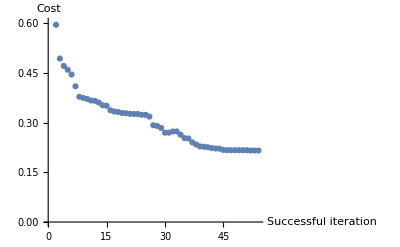

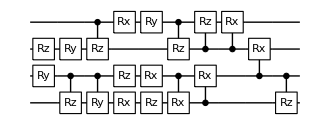

prob(0):<|0→0.24155,1→0.26711,2→0.258718,3→0.232622|>

dist_fid=0.394233

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 06:46:26, fev:312, <E>: 0.2183893811698448 nansatz: 14 merged-smallθ-metric-bf-gmerged: {0, 17, 0, 0, 10}

@cycle2:Sat 17 Sep 2022 06:47:37, fev:450, <E>: 0.192187228904199 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 13}

I'm slowing down @cycle 3

@cycle3:Sat 17 Sep 2022 06:47:58, fev:483, <E>: 0.192187228904199 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 17}

I'm slowing down @cycle 4

@cycle4:Sat 17 Sep 2022 06:48:59, fev:522, <E>: 0.192187228904199 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 31, 0, 0, 23}

compile time:30.5709 minutes; total iterations 624

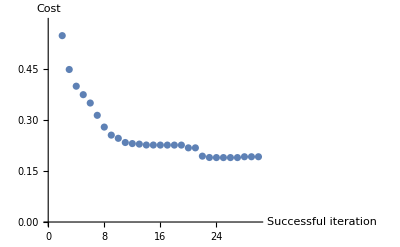

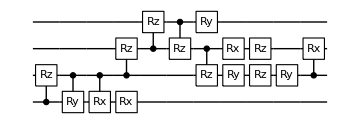

prob(0):<|0→0.238605,1→0.264361,2→0.237539,3→0.259495|>

dist_fid=0.417229

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 06:53:09, fev:256, <E>: 0.42668069588887525 nansatz: 27 merged-smallθ-metric-bf-gmerged: {0, 3, 0, 1, 12}

@cycle2:Sat 17 Sep 2022 06:57:39, fev:484, <E>: 0.3297174499331912 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 29, 1, 1, 16}

I'm slowing down @cycle 3

@cycle3:Sat 17 Sep 2022 06:58:30, fev:531, <E>: 0.3297174499331912 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 29, 1, 1, 26}

I'm slowing down @cycle 4

@cycle4:Sat 17 Sep 2022 06:59:59, fev:577, <E>: 0.3297174499331912 nansatz: 17 merged-smallθ-metric-bf-gmerged: {0, 29, 1, 1, 35}

compile time:109.585 minutes; total iterations 711

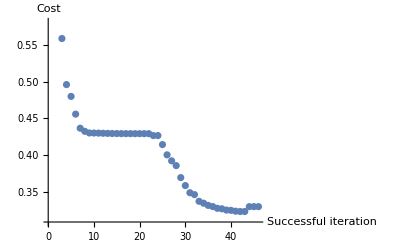

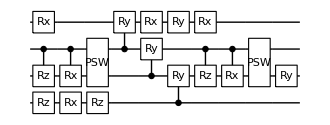

prob(0):<|0→0.25561,1→0.230839,2→0.265876,3→0.247675|>

dist_fid=0.794156

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 07:03:15, fev:228, <E>: 0.17278501227822501 nansatz: 14 merged-smallθ-metric-bf-gmerged: {1, 16, 0, 0, 13}

@cycle2:Sat 17 Sep 2022 07:04:14, fev:341, <E>: 0.1618226452386669 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 24, 0, 0, 19}

@cycle3:Sat 17 Sep 2022 07:05:17, fev:449, <E>: 0.13767626627769108 nansatz: 17 merged-smallθ-metric-bf-gmerged: {1, 38, 0, 0, 24}

@cycle4:Sat 17 Sep 2022 07:06:17, fev:554, <E>: 0.13073307198692352 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 49, 0, 0, 29}

I'm slowing down @cycle 5

@cycle5:Sat 17 Sep 2022 07:06:47, fev:593, <E>: 0.13073307198692352 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 49, 0, 0, 33}

I'm slowing down @cycle 6

@cycle6:Sat 17 Sep 2022 07:07:55, fev:635, <E>: 0.13073307198692352 nansatz: 18 merged-smallθ-metric-bf-gmerged: {1, 49, 0, 0, 39}

compile time:38.6258 minutes; total iterations 782

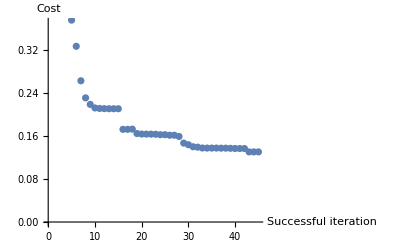

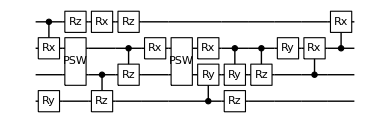

prob(0):<|0→0.245338,1→0.257945,2→0.260433,3→0.236284|>

dist_fid=0.249115

Compilation with automatically generated ansatz

@cycle1:Sat 17 Sep 2022 07:12:13, fev:251, <E>: 0.3951766846917847 nansatz: 18 merged-smallθ-metric-bf-gmerged: {0, 15, 0, 1, 14}

@cycle2:Sat 17 Sep 2022 07:17:28, fev:584, <E>: 0.26343755840497357 nansatz: 22 merged-smallθ-metric-bf-gmerged: {0, 29, 1, 2, 17}

@cycle3:Sat 17 Sep 2022 07:19:37, fev:706, <E>: 0.2412744114134524 nansatz: 25 merged-smallθ-metric-bf-gmerged: {0, 40, 1, 2, 18}

@cycle4:Sat 17 Sep 2022 07:22:21, fev:832, <E>: 0.2315456487593965 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 51, 1, 2, 23}

I'm slowing down @cycle 5

@cycle5:Sat 17 Sep 2022 07:24:19, fev:904, <E>: 0.2315456487593965 nansatz: 28 merged-smallθ-metric-bf-gmerged: {0, 51, 1, 2, 27}

@cycle6:Sat 17 Sep 2022 07:29:53, fev:1052, <E>: 0.22285249597814308 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 73, 1, 2, 36}

I'm slowing down @cycle 7

@cycle7:Sat 17 Sep 2022 07:32:00, fev:1099, <E>: 0.22285249597814308 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 73, 1, 2, 45}

I'm slowing down @cycle 8

@cycle8:Sat 17 Sep 2022 07:35:43, fev:1143, <E>: 0.22285249597814308 nansatz: 32 merged-smallθ-metric-bf-gmerged: {0, 73, 1, 2, 55}

compile time:287.075 minutes; total iterations 1579

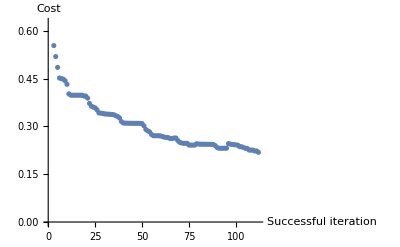

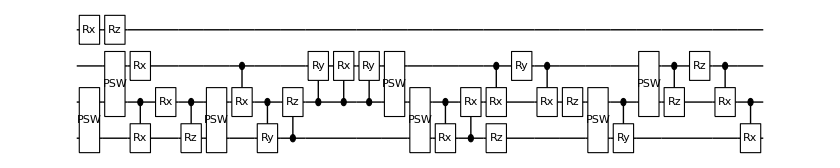

prob(0):<|0→0.239202,1→0.252989,2→0.254916,3→0.252893|>

dist_fid=0.599889

```mathematica
unitary=CalcCircuitMatrix@QFT@qubitsnum;
dev=ToyDevice[];
toy2={};
Table[
conf=checkedConf[dev,unitary,nt];
CompileCirc[conf,unitary,qubitsnum,toy2]
,{5}];
```